## Financial Data

```mathematica
FinancialData["AMZN", "Lookup"]//FullForm
```

List["NASDAQ:AMZN"]

```mathematica
FinancialData["NASDAQ:AMZN"]
```

1 823.28 $

```mathematica
a$=FinancialData["NASDAQ:AMZN",{DateObject[{2009},"Year","Gregorian",-7.],DateObject[]}]
```

TimeSeries[…]

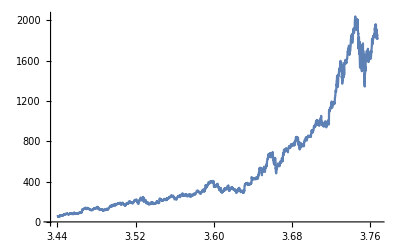

```mathematica
ListLinePlot[a$]
```

```mathematica
a$=FinancialData["NASDAQ:AMZN",{DateObject[{2019,3}],DateObject[]}]
```

TimeSeries[…]

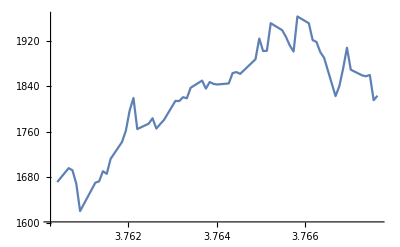

```mathematica
ListLinePlot[a$]
```

```mathematica
p$=Predict[
MapThread[Rule,{
AbsoluteTime@*First/@a$["DatePath"],
QuantityMagnitude/@a$["Values"]}],
Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
Information[p$]
```

Predictor information
Data type | Numerical
Standard deviation | 37.4 ± 7.3
Method | GaussianProcess
Single evaluation time | 2.8 ms/example
Batch evaluation speed | 58.4 examples/ms
Loss | 11.3 ± 2.6
Model memory | 129. kB
Training examples used | 59 examples
Training time | 800. ms
 |

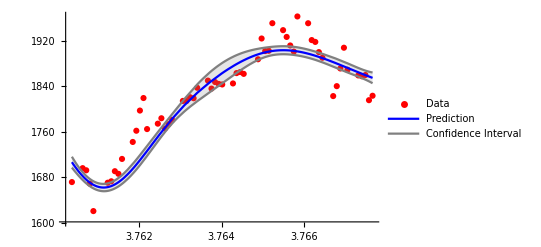

```mathematica
Show[
ListPlot[
MapThread[List,{
AbsoluteTime@*First/@a$["DatePath"],
QuantityMagnitude/@a$["Values"]}],
PlotStyle->Red,
PlotLegends->{"Data"}],
Plot[{
p$[t],
p$[t]+StandardDeviation[p$[t,"Distribution"]],p$[t]-StandardDeviation[p$[t,"Distribution"]]},
{t,
AbsoluteTime[First[First[a$["DatePath"]]]],
AbsoluteTime[First[Last[a$["DatePath"]]]]},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}]   ]
```

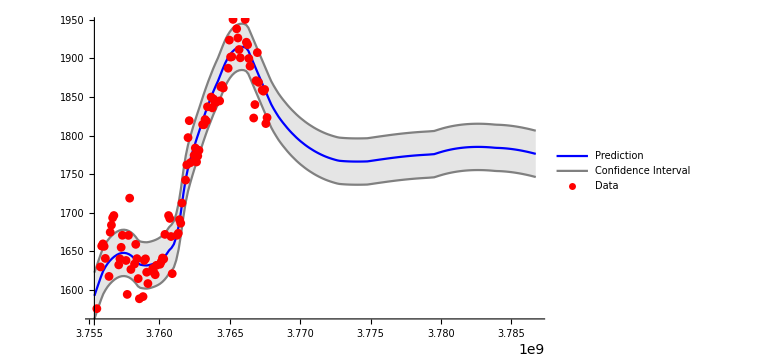
-Graphics-
NormalDistribution[1776.16,30.043]
Predictor information
Data type | Numerical
Standard deviation | 44. ± 6.9
Method | NeuralNetwork
Single evaluation time | 3.15 ms/example
Batch evaluation speed | 16.5 examples/ms
Loss | 5.18 ± 0.14
Model memory | 294. kB
Training examples used | 99 examples
Training time | 28.8 s
 |

```mathematica
ClearAll[predictPrices];
predictPrices[instrumentSymbol_String,
closingPriceDateStart_,
closingPriceDateEnd_,
predictionEnd_,
method_String]:=
With[{
data=FinancialData[
instrumentSymbol,
{closingPriceDateStart,closingPriceDateEnd}],
absEnd=AbsoluteTime@predictionEnd},
With[{
absTimes=AbsoluteTime@*First/@data["DatePath"],
absPrices=QuantityMagnitude/@data["Values"]},
With[{
points=MapThread[List,{absTimes,absPrices}],
predictor=Predict[
MapThread[Rule,{absTimes,absPrices}],
Method->method
]},
Information[predictor];
Column[{
Show[
Plot[{
predictor[t],
predictor[t]+StandardDeviation[predictor[t,"Distribution"]],predictor[t]-StandardDeviation[predictor[t,"Distribution"]]},
{t,
AbsoluteTime[First[First[data["DatePath"]]]],
absEnd},
ImageSize->Large,
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],
ListPlot[points,
PlotStyle->Red,
PlotLegends->{"Data"}]],
predictor[absEnd,"Distribution"],
Information[predictor]
}]
]]];
predictPrices[
"AMZN",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}],
"NeuralNetwork"]
```

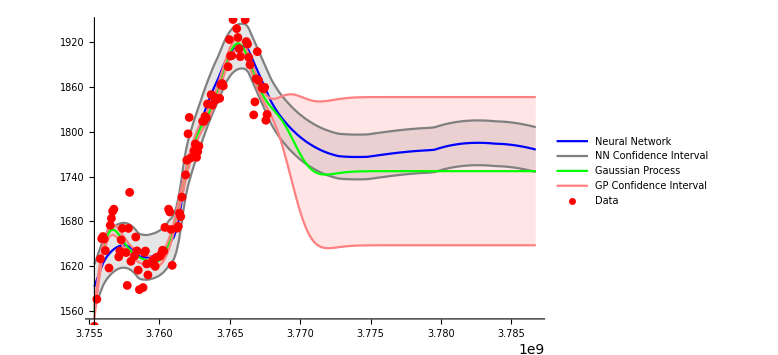
-Graphics-
Predictor information
Data type | Numerical
Standard deviation | 44. ± 6.9
Method | NeuralNetwork
Single evaluation time | 3.23 ms/example
Batch evaluation speed | 12.2 examples/ms
Loss | 5.18 ± 0.14
Model memory | 300. kB
Training examples used | 99 examples
Training time | 31.8 s
 | 
Predictor information
Data type | Numerical
Standard deviation | 48.1 ± 21.
Method | GaussianProcess
Single evaluation time | 6.25 ms/example
Batch evaluation speed | 13.4 examples/ms
Loss | 10.6 ± 3.3
Model memory | 187. kB
Training examples used | 99 examples
Training time | 2.02 s
 |

```mathematica
ClearAll[predictPrices];
predictPrices[instrumentSymbol_String,
closingPriceDateStart_,
closingPriceDateEnd_,
predictionEnd_]:=
With[{data=FinancialData[instrumentSymbol,
{closingPriceDateStart,closingPriceDateEnd}],
absEnd=AbsoluteTime@predictionEnd},
With[{absTimes=AbsoluteTime@*First/@data["DatePath"],
absPrices=QuantityMagnitude/@data["Values"]},
With[{points=MapThread[List,{absTimes,absPrices}],
rules=MapThread[Rule,{absTimes,absPrices}]},
With[{nnp=Predict[rules,Method->"NeuralNetwork",
PerformanceGoal->"Quality"],
gpp=Predict[rules,Method->"GaussianProcess",PerformanceGoal->"Quality"]},
Column[{   Show[   Plot[{
nnp[t],
nnp[t]+StandardDeviation[nnp[t,"Distribution"]],nnp[t]-StandardDeviation[nnp[t,"Distribution"]],
gpp[t],
gpp[t]+StandardDeviation[gpp[t,"Distribution"]],gpp[t]-StandardDeviation[gpp[t,"Distribution"]]},
{t,AbsoluteTime[First[First[data["DatePath"]]]],absEnd},
ImageSize->Large,
PlotStyle->{Blue,Gray,Gray,Green,Pink,Pink},
Filling->{2->{3},5->{6}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{
"Neural Network","NN Confidence Interval", "", 
"Gaussian Process", "GP Confidence Interval",""}],
ListPlot[points,PlotStyle->Red,PlotLegends->{"Data"}]],
Information[nnp],Information[gpp]
}]
]]]];
predictPrices[
"AMZN",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}]]
```

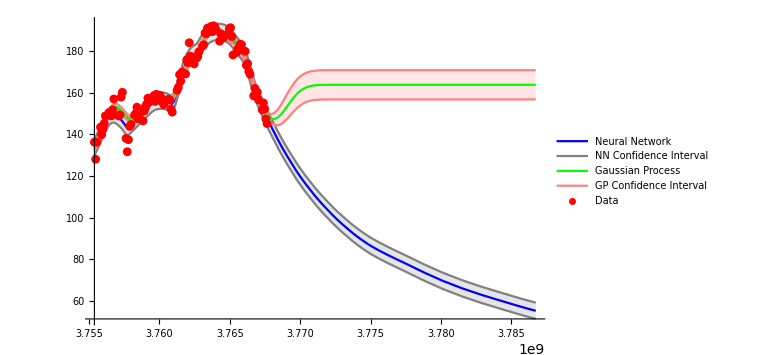
-Graphics-
Predictor information
Data type | Numerical
Standard deviation | 6.35 ± 1.1
Method | NeuralNetwork
Single evaluation time | 3.14 ms/example
Batch evaluation speed | 11.6 examples/ms
Loss | 3.34 ± 0.27
Model memory | 317. kB
Training examples used | 99 examples
Training time | 23.1 s
 | 
Predictor information
Data type | Numerical
Standard deviation | 8.07 ± 1.5
Method | GaussianProcess
Single evaluation time | 6.15 ms/example
Batch evaluation speed | 12.8 examples/ms
Loss | 19.6 ± 12.
Model memory | 185. kB
Training examples used | 99 examples
Training time | 4.2 s
 |

```mathematica
predictPrices[
"NVIDIA",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}]]
```

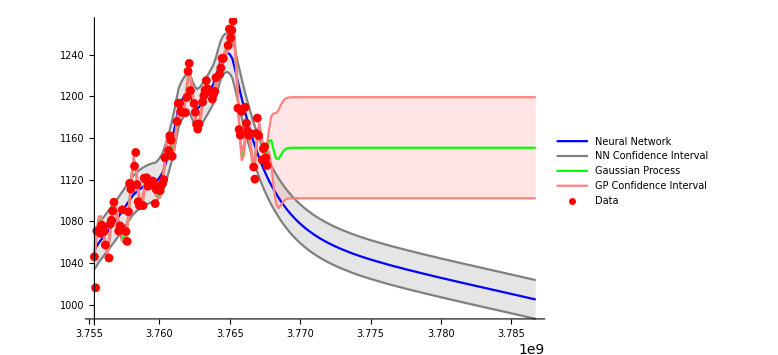

```mathematica
ClearAll[predictPrices];
predictPrices[instrumentSymbol_String,
closingPriceDateStart_,
closingPriceDateEnd_,
predictionEnd_]:=
With[{data=FinancialData[instrumentSymbol,
{closingPriceDateStart,closingPriceDateEnd}],
absEnd=AbsoluteTime@predictionEnd},
With[{absTimes=AbsoluteTime@*First/@data["DatePath"],
absPrices=QuantityMagnitude/@data["Values"]},
With[{points=MapThread[List,{absTimes,absPrices}],
rules=MapThread[Rule,{absTimes,absPrices}]},
With[{nnp=Predict[rules,Method->"NeuralNetwork",
PerformanceGoal->"Quality"],
gpp=Predict[rules,Method->"GaussianProcess",PerformanceGoal->"Quality"]},
Column[{   Show[   Plot[{
nnp[t],
nnp[t]+StandardDeviation[nnp[t,"Distribution"]],nnp[t]-StandardDeviation[nnp[t,"Distribution"]],
gpp[t],
gpp[t]+StandardDeviation[gpp[t,"Distribution"]],gpp[t]-StandardDeviation[gpp[t,"Distribution"]]},
{t,AbsoluteTime[First[First[data["DatePath"]]]],absEnd},
ImageSize->Large,
PlotStyle->{Blue,Gray,Gray,Green,Pink,Pink},
Filling->{2->{3},5->{6}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{
"Neural Network","NN Confidence Interval", "", 
"Gaussian Process", "GP Confidence Interval",""}],
ListPlot[points,PlotStyle->Red,PlotLegends->{"Data"}]]
}]
]]]];
predictPrices[
"GOOG",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}]]
```

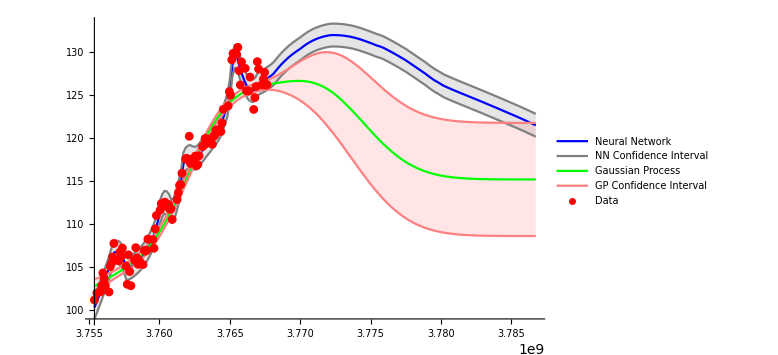

```mathematica
predictPrices[
"MSFT",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}]]
```

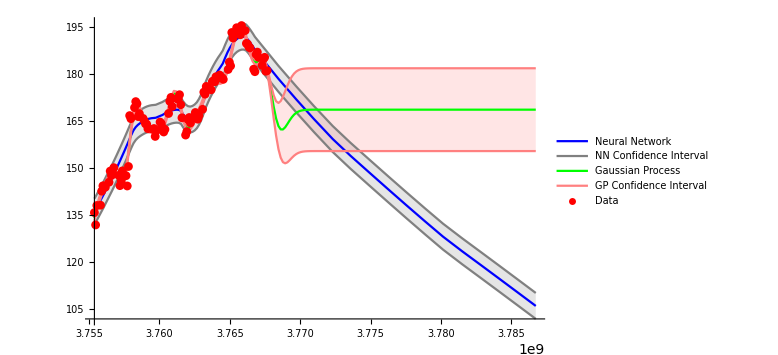

```mathematica
predictPrices[
"Facebook",
DateObject[{2019}],
DateObject[],
DateObject[{2019,12,31}]]
```